## Parameters

```mathematica
wd=NotebookDirectory[];
SetDirectory[wd];
(*Read parameter file into conf*)
readConf[filename_]:=Module[{res={},i,rawF,Ln,chk},
rawF=ReadList[filename,"String"];
Print[Length[rawF]];
For[i=1,i<=Length[rawF],++i,
If[rawF[[i]]=={},Continue[]];
If[StringTake[rawF[[i]],1]=="#",Continue[]];
Ln=StringSplit[rawF[[i]]];
If[NumericQ[ToExpression[Ln[[2]]]],AppendTo[res,Ln[[1]]->ToExpression[Ln[[2]]]],AppendTo[res,Ln[[1]]->Ln[[2]]]];
];
Association[res]
];
(*Parameters can be called same as in py*)
conf=readConf["../params"];
StateList={"1S"};
```

68

```mathematica
conf
```

<|L→50,dt→0.1,T→0.12,tFn→1000,NY→1,Nbb→10000,ECut→20,prCut→10,NPts→100,ExportRates→True,NXPart→10,NThreads→14,HydroMode→0,HPts→20,Mb→4.65,M1S→9.46,M2S→10.023,E1S→0.13,E2S→0.723,bsig→0.01,Ysig→0.02,alphaS→0.3,CF→1.3333333333333333333,NC→3,gs→0.75,Ch→0,rateFile→bottom_rates_2d.tsv,boop→gleep|>

### Matrix Elements

```mathematica
η[prel_,st_]:=conf["alphaS"]*conf["M"<>st]/(4*conf["NC"]*prel)
aB[st_]:=2/(conf["alphaS"]*conf["CF"]*conf["M"<>st]);
(*Matrix Elements*)
MOvLp[prel_,st_]:=Piecewise[{{
(((2^9)(Pi^2)(η[prel,st])(aB[st]^7)(prel^2)(1+η[prel,st]^2)(2+η[prel,st]*aB[st]*prel)^2)/((1+(aB[st]^2)(prel^2))^6(Exp[2Pi*η[prel,st]]-1)))*Exp[4η[prel,st]*ArcTan[aB[st]*prel]],st=="1S"},
{
(((2^18)(Pi^2)(η[prel,st])(aB[st]^7)(prel^2)(1+η[prel,st]^2))/((1+4(aB[st]^2)(prel^2))^6(Exp[2Pi*η[prel,st]]-1)))*Exp[4η[prel,st]*ArcTan[2aB[st]*prel]],st=="2S"}}];
MOvLp[prel_,st_]:=Piecewise[{{
(((2^10)(Pi)(aB[st]^7)(prel^2)))/((1+(aB[st]^2)(prel^2))^6),st=="1S"},
{
((2^21)(Pi)(aB[st]^7)(prel^2)(1-2(aB[st]^2)(prel^2))^2)/((1+4(aB[st]^2)(prel^2))^8),st=="2S"}}];
```

## Dissociation Channels

### Real Gluon Absorption

```mathematica
(*Sampling integrand*)
Ig[q_,st_]:=Piecewise[{{(q^3)*Sqrt[conf["M"<>st](q-conf["E"<>st])](1/(Exp[q/conf["T"]]-1))MOvLp[Sqrt[conf["M"<>st](q-conf["E"<>st])],st],q>conf["E"<>st]},{0,q<=conf["E"<>st]}}];
(*IgMaxs=Table[Maximize[{Ig[q,StateList[[i]]],conf["E"<>StateList[[i]]]<q<20*conf["E"<>StateList[[i]]]},q][[1]],{i,1,Length[StateList]}];*)
Igs=Table[Ig[q,StateList[[i]]],{i,1,Length[StateList]}];
```

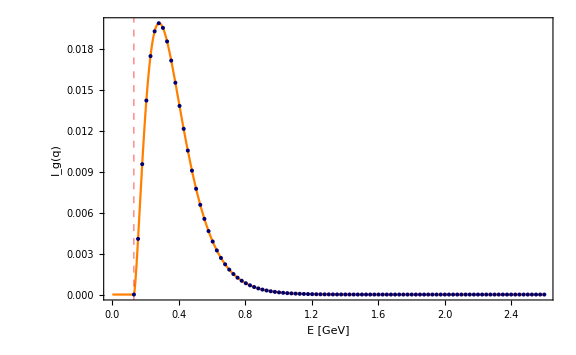

```mathematica
RGAIntPlot=Plot[Igs,{q,0,20*conf["E1S"]},PlotRange->All,PlotStyle->{Directive[Blue],Directive[Orange]},Frame->True,FrameLabel->{{"I_g(q)",""},{"E [GeV]","RGA Integrand"}},ImageSize->Large,GridLines->{Table[conf["E"<>StateList[[i]]],{i,1,Length[StateList]}],None},GridLinesStyle->Directive[Red,Dashed]];
IgDat=Table[Transpose[{Range[conf["E1S"],20*conf["E"<>StateList[[i]]],(19*conf["E"<>StateList[[i]]])/(conf["NPts"]-1)],Flatten[Import["../export/rateRGA_"<>StateList[[i]]<>".tsv"]]}],{i,1,1}];
expRGAIntPlot=ListPlot[IgDat,PlotStyle->{Directive[{PointSize->0.005,Darker[Darker[Blue]]}],Directive[{PointSize->0.001,Darker[Orange]}]},Frame->True,FrameLabel->{{"I_g(q)",""},{"E [GeV]","RGA Integrand"}},ImageSize->Large];
Show[RGAIntPlot,expRGAIntPlot]
```

## Regeneration Channels

### Real Gluon Radiation

```mathematica
(*RGR rate for a given pair*)
```

```mathematica
RGRRate[x_,prel_,st_]:=(Exp[-(x^2)/(2aB[st]^2)]/(2Pi*aB[st]^2)^(3/2))(8/9)conf["alphaS"](((prel^2/conf["M"<>st])+conf["E"<>st])^3)*(2+(2/(Exp[((prel^2/conf["M"<>st])+conf["E"<>st])/conf["T"]]-1)))*MOvLp[prel,st];
RGRRatePlot1S=Plot3D[RGRRate[x,p,"1S"](conf["gs"]/(conf["NC"]^2)),{x,0,3},{p,0.1,conf["prCut"]},ScalingFunctions->"Log",AxesLabel->{"|x_i-x_j|","p_rel","(Γ^RGR)_ij"},Ticks->{Automatic,Automatic,Automatic},PlotRange->All,PlotStyle->Directive[Blue,Opacity[0.4]]];
```

```mathematica
RGRRaw=Table[Import["../export/rateRGR_"<>StateList[[i]]<>".tsv"],{i,1,Length[StateList]}];
RGRDat=Table[Table[Table[{(ix-1)(2*conf["L"]*Sqrt[3]/conf["NXPart"])/(conf["NPts"]-1),(jp-1)(conf["prCut"])/(conf["NPts"]-1),RGRRaw[[s,ix,jp]]},{ix,1,conf["NPts"]}],{jp,1,conf["NPts"]}],{s,1,Length[StateList]}];
expRGRRatePlot1S=ListPointPlot3D[Flatten[RGRDat[[1]],1],ScalingFunctions->"Log",PlotRange->All,PlotStyle->Red];
PRC=conf["prCut"];
XSC=2;
CutoffLinesPlot1S=ListPointPlot3D[{Table[{x,PRC,RGRRate[x,PRC,"1S"]},{x,0,2,0.01}],Table[{XSC,p,RGRRate[XSC,p,"1S"]},{p,0.5,conf["prCut"],0.1}]},PlotStyle->{Green,Green},ScalingFunctions->"Log"];
Show[RGRRatePlot1S,expRGRRatePlot1S,CutoffLinesPlot1S]
```

-Graphics3D-

```mathematica
RGRintTot1S=NIntegrate[RGRRate[x,p,"1S"],{x,0,2*conf["L"]},{p,0,100}](*Total rate integrated over x and prel*)
RGRremoved1S=NIntegrate[RGRRate[x,p,"1S"],{x,2,2*conf["L"]},{p,0,100}]+NIntegrate[RGRRate[x,p,"1S"],{x,0,2*conf["L"]},{p,20,100}](*Chunks that are removed by cutoffs (which have cutoffs themselves but numerical integration has its... limits...)*)
```

0.148145

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.000586119

```mathematica
RGRremoved1S/RGRintTot1S
```

0.00395638

```mathematica
(*Cutoffs of |xi-xj|=2 and prCut=20 would only neglect <this much of the total rate (this double counts part but its also the smallest part) *)
```

## Other

### Hydro background

### Lorentz Boosting

```mathematica
Λ[v_]:={{(1/Sqrt[1-v.v]),-(1/Sqrt[1-v.v])v[[1]],-(1/Sqrt[1-v.v])v[[2]],-(1/Sqrt[1-v.v])v[[3]]},
{-(1/Sqrt[1-v.v])v[[1]],1+((1/Sqrt[1-v.v])-1)(v[[1]]^2)/(v.v),((1/Sqrt[1-v.v])-1)v[[1]]*v[[2]]/(v.v),((1/Sqrt[1-v.v])-1)v[[1]]*v[[3]]/(v.v)},
{-(1/Sqrt[1-v.v])v[[2]],((1/Sqrt[1-v.v])-1)v[[2]]*v[[1]]/(v.v),1+((1/Sqrt[1-v.v])-1)(v[[2]]^2)/(v.v),((1/Sqrt[1-v.v])-1)v[[2]]*v[[3]]/(v.v)},
{-(1/Sqrt[1-v.v])v[[3]],((1/Sqrt[1-v.v])-1)v[[3]]*v[[1]]/(v.v),((1/Sqrt[1-v.v])-1)v[[3]]*v[[2]]/(v.v),1+((1/Sqrt[1-v.v])-1)(v[[3]]^2)/(v.v)}};
FullSimplify[Λ[{vx,vy,vz}].{En,px,py,pz}]
```

{-(-En+px vx+py vy+pz vz)/(√(1-vx^2-vy^2-vz^2)),(px (vx^2+√(1-vx^2-vy^2-vz^2) (vy^2+vz^2))-vx (En (vx^2+vy^2+vz^2)+(py vy+pz vz) (-1+√(1-vx^2-vy^2-vz^2))))/(√(1-vx^2-vy^2-vz^2) (vx^2+vy^2+vz^2)),(px vx vy-px vx vy √(1-vx^2-vy^2-vz^2)-En vy (vx^2+vy^2+vz^2)-pz vy vz (-1+√(1-vx^2-vy^2-vz^2))+py (vy^2+√(1-vx^2-vy^2-vz^2) (vx^2+vz^2)))/(√(1-vx^2-vy^2-vz^2) (vx^2+vy^2+vz^2)),(px vx vz+py vy vz-(px vx+py vy) vz √(1-vx^2-vy^2-vz^2)-En vz (vx^2+vy^2+vz^2)+pz (vz^2+(vx^2+vy^2) √(1-vx^2-vy^2-vz^2)))/(√(1-vx^2-vy^2-vz^2) (vx^2+vy^2+vz^2))}

## Expected Values

```mathematica
rEp[p_,M_]:=Sqrt[M^2+p.p];
cEp[p_,M_]:=M+p.p/(2*M);
```

```mathematica
(*w/o λ*)
cNeqb=(6*conf["L"]^3)(1/(2Pi)^3)*Integrate[Exp[-cEp[{px,py,pz},conf["Mb"]]/conf["T"]],{px,0,Infinity},{py,0,Infinity},{pz,0,Infinity}]
cNeqY=(3*conf["L"]^3)(1/(2Pi)^3)*Integrate[Exp[-cEp[{px,py,pz},conf["M1S"]]/conf["T"]],{px,0,Infinity},{py,0,Infinity},{pz,0,Infinity}]
rNeqb=(6*conf["L"]^3)(1/(2Pi)^3)*NIntegrate[Exp[-rEp[{px,py,pz},conf["Mb"]]/conf["T"]],{px,0,Infinity},{py,0,Infinity},{pz,0,Infinity}]
rNeqY=(3*conf["L"]^3)(1/(2Pi)^3)*NIntegrate[Exp[-rEp[{px,py,pz},conf["M1S"]]/conf["T"]],{px,0,Infinity},{py,0,Infinity},{pz,0,Infinity}]
```

3.6791×10^-14

2.0864×10^-31

3.85911×10^-14

2.1363×10^-31

```mathematica
cλ=Solve[cNeqY*λ^2+cNeqb*λ-(conf["Nbb"]+conf["NY"])==0,λ][[2,1,2]]
rλ=Solve[rNeqY*λ^2+rNeqb*λ-(conf["Nbb"]+conf["NY"])==0,λ][[2,1,2]]
```

1.47857×10^17

1.4414×10^17

```mathematica
(-cNeqb+Sqrt[cNeqb^2-4*cNeqY*(-(conf["Nbb"]+conf["NY"]))])/(2*cNeqY)
```

1.47857×10^17

```mathematica
(*Classical*)
cNeqY*cλ^2
cNeqb*cλ
cNeqY*cλ^2/(cNeqY*cλ^2+cNeqb*cλ)
```

4561.21

5439.79

0.456075

```mathematica
(*Relativistic*)
rNeqY*cλ^2
rNeqb*cλ
rNeqY*rλ^2/(rNeqY*rλ^2+rNeqb*rλ)
```

4670.29

5705.95

0.443802

```mathematica
(6*conf["L"]^3)(1/(2Pi)^3)*Integrate[Exp[-cEp[{px,py,pz},conf["Mb"]]/conf["T"]],{px,0,Infinity},{py,0,Infinity},{pz,0,Infinity}]
```

3.6791×10^-14

```mathematica
(6*conf["L"]^3)(1/(2Pi)^3)*Integrate[Exp[-cEp[{px,py,pz},conf["Mb"]]/conf["T"]],{px,0,1},{py,0,1},{pz,0,1}]
```

2.02358×10^-14

2.80315×10^-17

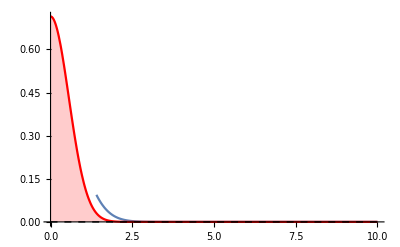

```mathematica
(*Momentum Distribution*)

fB1[px_,M_,T_]:=Exp[-Sqrt[px^2+M^2]/T];
NC=NIntegrate[fB1[px,conf["M"<>st],conf["T"]],{px,-Infinity,Infinity}]
SigM[M_,T_]:=M*T;
st="b";
MaxR=10;
Show[Plot[fB1[px,conf["M"<>st],conf["T"]]/NC,{px,0,MaxR}],Plot[gPDF[x,0,SigM[conf["M"<>st],conf["T"]]],{x,0,MaxR},PlotRange->All,AxesLabel->{"x","PDF"},Filling->Axis,PlotStyle->Red],Plot[(fB1[px,conf["M"<>st],conf["T"]]/NC)/gPDF[px,0,SigM[conf["M"<>st],conf["T"]]],{px,0,MaxR},PlotStyle->Black,PlotRange->All],PlotRange->All,Epilog->{Directive[{Black,Dashed}],Line[{{0,0},{MaxR,0}}]}]
```

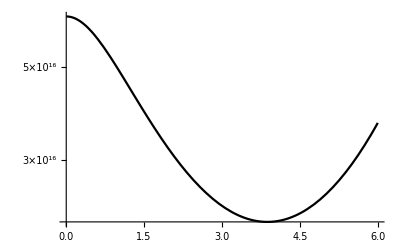

```mathematica
LogPlot[(fB1[px,1,1]/NC)/gPDF[px,0,2],{px,0,6},PlotStyle->Black]
```

```mathematica
NIntegrate[fB[px,py,pz,1,1],{px,-Infinity,Infinity},{py,-Infinity,Infinity},{pz,-Infinity,Infinity}]
```

NIntegrate::inumr: The integrand fB[px,py,pz,1,1] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.},{-∞,0.},{-∞,0.}}.

NIntegrate[fB[px,py,pz,1,1],{px,-∞,∞},{py,-∞,∞},{pz,-∞,∞}]

```mathematica
fB[px_,py_,M_,T_]:=Exp[-Sqrt[px^2+py^2+M^2]/T];
```

```mathematica
NIntegrate[fB1[px,1,1],{px,-Infinity,Infinity}]
```

1.20381

```mathematica
gPDF[x_,mu_,sigma_]:=1/(sigma Sqrt[2 Pi]) Exp[-(x-mu)^2/(2 sigma^2)];
```

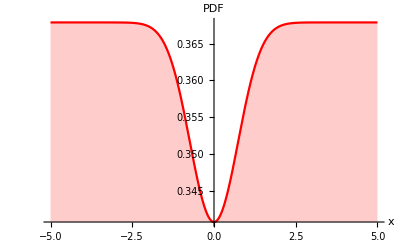

```mathematica
Plot[fB1[gPDF[x,0,1],1,1],{x,-5,5},PlotRange->All,AxesLabel->{"x","PDF"},Filling->Axis,PlotStyle->Red]
```

```mathematica
NIntegrate[fB1[px,conf["M1S"],conf["T"]]/NC,{px,-Infinity,Infinity}]
```

5.5482×10^-18

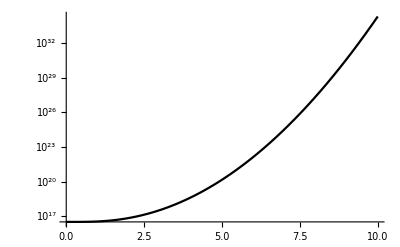

```mathematica
LogPlot[(fB1[px,1,1]/NC)/gPDF[px,0,SigM[1,1]],{px,0,MaxR},PlotStyle->Black,PlotRange->All,Epilog->{Directive[{Black,Dashed}],Line[{{0,1},{MaxR,1}}]}]
```

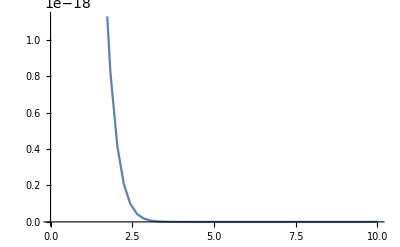

```mathematica
Plot[fB1[px,conf["M"<>st],conf["T"]],{px,0,MaxR}]
```